```mathematica
S3Draw[R_,S_,T_,P_,q_,c_,n_]:=
(*
R,S,T,P represent the payoffs in a stage game: p(CC)=R, p(CD)=S, p(DC)=T, p(DD)=P. q is the probability that a pair of co-players part from each other in the next round by accident. c is the cost to search and form a new pair. n controls the resolution of the simplex graph.
*)
(coords[{x_,y_,z_}]:={x/2+y,x Tan[Pi/3]/2};
(* This is the function to project 3d data to a simplex on 2d triangle space. *)
xlist={};
(* Set up an empty array *)
For[i=1,i≤n,i++,
For[j=1;x1=i/n,j<n-i,j++,x2=j/n;x3=1-x1-x2;xlist=Append[xlist,{x1,x2,x3}]
]
];
(* Uniformly distributed points in a 3D space limited by x+y+z=1, x≥0, y≥0, z≥0. *)
frame=Graphics[{Thick,Line[{{0,0},{1,0},{0.5,Sqrt[3]/2},{0,0}}]},ImageSize->300];
(* The frame of a simplex *)
vertices=Graphics[{Text[Style["BC",Medium,Bold],{0-0.02,0-0.02}],Text[Style["NC",Medium,Bold],{1+0.02,0-0.02}],Text[Style["D",Medium,Bold],{0.5,√3/2+0.02}]},ImageSize->300];
(* Label the three vertices of a simplex *)

s={s1,s2,s3};
Q={{1,1,1},{1,1,1},{1,1,q}};
U={{P,T,T},{S,R,R},{S,R,R}}-c*(ConstantArray[1,{3,3}]-Q);
W=Table[Total[s U[[i]]/Q[[i]]]/Total[s/Q[[i]]],{i,3}];
wbar=Total[Table[s[[i]] s[[j]],{i,3},{j,3}] U/Q,Infinity]/Total[s];
(* The mean fitness of each type of player at equilibrium *)

s3ofx=Solve[x3==(s3 (1-x3+s3/q))/(1-x3+s3),s3];

wlist=Table[W/.{s1->xlist[[i,1]],s2->xlist[[i,2]],s3ofx[[2,1]]/.x3->xlist[[i,3]]},{i,Length[xlist]}];
(* Compute the fitness of each type of player except type 1 as we assume x1 = 0 here. *)

wbarlist=Total[Transpose[wlist*xlist]];
(* Mean fitness of the three types of players (2, 3, 4) *)
gradient3d=xlist*(wlist/wbarlist-1);
(* Compute the gradient at each point in a 3D space according to the replicator equation. *)
simdata=coords[#]& /@xlist;
(* Project the points from 3D to a simplex *)
simvector=coords[#]& /@gradient3d;
(* Project the gradients from 3D to a simplex *)
vector=Table[{simdata[[i]],simvector[[i]]},{i,Length[simdata]}];
(* Group each point with the corresponding gradient *)

vectorfield=ListVectorPlot[vector,VectorPoints->simdata,Frame->False];
streamplot=ListStreamPlot[vector,StreamPoints->simdata,Frame->False,RegionFunction->Function[{x,y},Sqrt[3]*x+y<Sqrt[3] && y<Sqrt[3]*x]];
Show[frame,vertices,vectorfield, ImageSize->600]
Show[frame,vertices,streamplot, ImageSize->600]
)
```

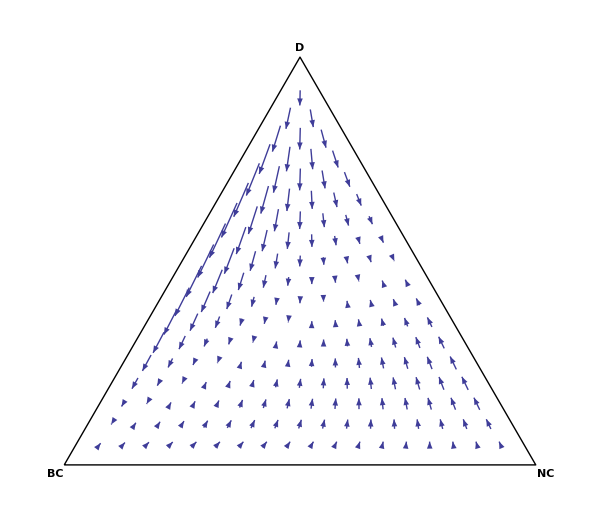
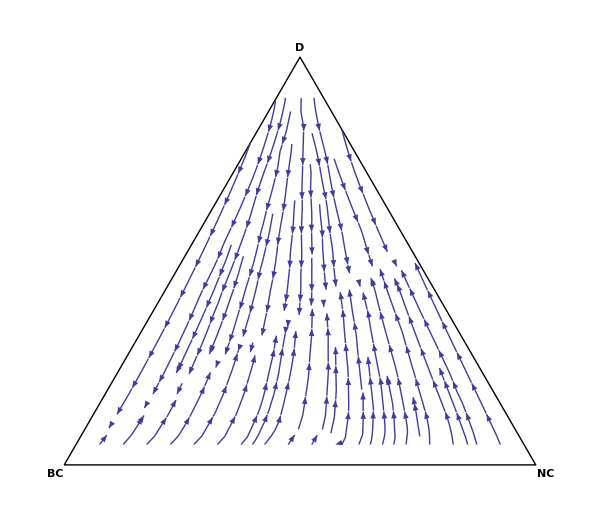

```mathematica
S3Draw[1,.8,1.2,.6,.2,.1,20]
```

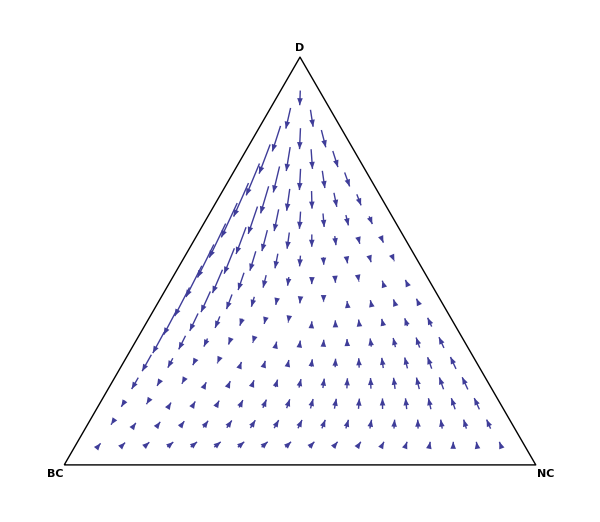
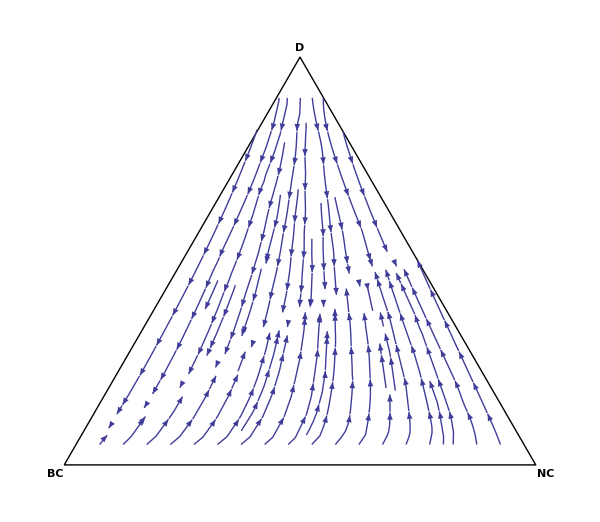

```mathematica
S3Draw[1,.8,1.2,.6,.1,.1,20]
```

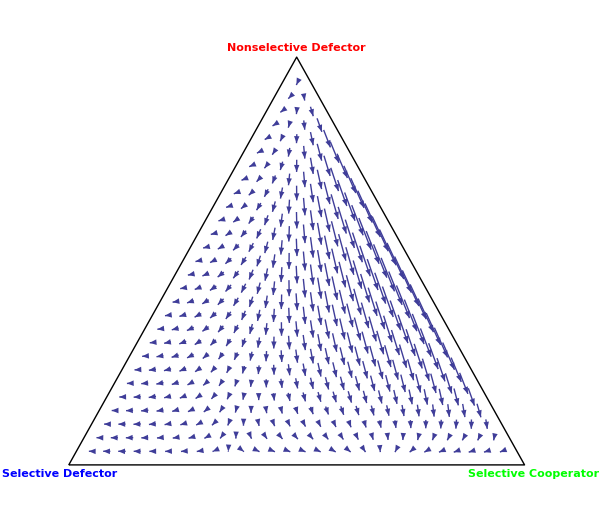
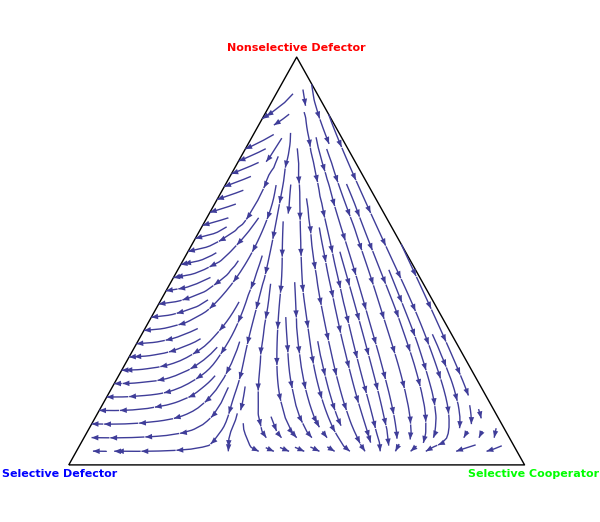

```mathematica
Simplex3Draw[4,2,5,3,.1,0,30]
```